```mathematica
ClearAll["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c U[x]-q U[x]^3+(3/2) q U[x] V[x]-(q/4) U''[x] ,
-c V[x]+(3/4) q V[x]^2-3 q U[x]^2 V[x]+(3 q/4) (U'[x])^2+(3 q/2) U[x] U''[x]-(1/4) q V''[x] 
}/.{U-> Function[x,a0 +a1*P[x]+b1*P[x]^(-1)], V-> Function[x,c0 +c1*P[x]+c2*P[x]^2+d1*P[x]^(-1)+d2*P[x]^(-2)]};
```

```mathematica
(*使用约束方程进行替换*)
(*转换成关于P的多项式，忽略x*)
SubEqns = eqns/.{P'[x] -> k+P[x]^2}/.{P''[x]->2*P[x]*(k+P[x]^2)}/.{P[x]->P} ;
(*每一项乘上P四次方，变为正次的多项式*)
expandedEqns=Expand[SubEqns*P^4];
(* P 的各个次幂*)
coeffEqns=Flatten[CoefficientList[expandedEqns,P]];
(*列出方程组*)
eqnList=Thread[coeffEqns==0];
```

```mathematica
(*解代数决定方程组，得到关于 c,a0,a1,b0,b1,b2 的表达式*)
Clear[k,c]
(*添加附加约束条件*)
addConstraints={q!=0,a1 !=0};
solutions=Solve[Join[eqnList,addConstraints],{k,a0,a1,b1,c0,c1,c2,d1,d2}];
solutions//Column
```

{k→c/q,a0→0,a1→-1,b1→0,c0→c/q,c1→0,c2→1,d1→0,d2→0}
{k→(4 c)/q,a0→0,a1→-1/2,b1→0,c0→(2 c)/q,c1→0,c2→1/2,d1→0,d2→0}
{k→c/q,a0→-(ⅈ √c)/(2 √q),a1→-1/2,b1→0,c0→c/(2 q),c1→0,c2→1/2,d1→0,d2→0}
{k→c/q,a0→(ⅈ √c)/(2 √q),a1→-1/2,b1→0,c0→c/(2 q),c1→0,c2→1/2,d1→0,d2→0}
{k→(4 c)/q,a0→0,a1→1/2,b1→0,c0→(2 c)/q,c1→0,c2→1/2,d1→0,d2→0}
{k→c/q,a0→-(ⅈ √c)/(2 √q),a1→1/2,b1→0,c0→c/(2 q),c1→0,c2→1/2,d1→0,d2→0}
{k→c/q,a0→(ⅈ √c)/(2 √q),a1→1/2,b1→0,c0→c/(2 q),c1→0,c2→1/2,d1→0,d2→0}
{k→c/q,a0→0,a1→1,b1→0,c0→c/q,c1→0,c2→1,d1→0,d2→0}
{k→c/q,a0→0,a1→1/2,b1→-c/(2 q),c0→c/q,c1→0,c2→1/2,d1→0,d2→c^2/(2 q^2)}
{k→c/(4 q),a0→0,a1→1,b1→-c/(4 q),c0→c/(2 q),c1→0,c2→1,d1→0,d2→c^2/(16 q^2)}
{k→c/(4 q),a0→-(ⅈ √c)/(2 √q),a1→1/2,b1→-c/(8 q),c0→c/(4 q),c1→0,c2→1/2,d1→0,d2→c^2/(32 q^2)}
{k→c/(4 q),a0→(ⅈ √c)/(2 √q),a1→1/2,b1→-c/(8 q),c0→c/(4 q),c1→0,c2→1/2,d1→0,d2→c^2/(32 q^2)}
{k→c/(4 q),a0→-(ⅈ √c)/(2 √q),a1→-1/2,b1→c/(8 q),c0→c/(4 q),c1→0,c2→1/2,d1→0,d2→c^2/(32 q^2)}
{k→c/(4 q),a0→(ⅈ √c)/(2 √q),a1→-1/2,b1→c/(8 q),c0→c/(4 q),c1→0,c2→1/2,d1→0,d2→c^2/(32 q^2)}
{k→c/(4 q),a0→0,a1→-1,b1→c/(4 q),c0→c/(2 q),c1→0,c2→1,d1→0,d2→c^2/(16 q^2)}
{k→c/q,a0→0,a1→-1/2,b1→c/(2 q),c0→c/q,c1→0,c2→1/2,d1→0,d2→c^2/(2 q^2)}

```mathematica
(* 运行好的验证 *)
(*使用中间变量z，之后替换不会出错*)
Clear[v,u]
solU=u->Function[{x,t},a0 +a1*P[z]+b1*P[z]^(-1)]
solV=v->Function[{x,t},c0 +c1*P[z]+c2*P[z]^2+d1*P[z]^(-1)+d2*P[z]^(-2)]
```

u→Function[{x,t},a0+a1 P[z]+b1/P[z]]

v→Function[{x,t},c0+c1 P[z]+c2 P[z]^2+d1/P[z]+d2/P[z]^2]

```mathematica
(* 由k得到约束方程解的列表 要使用中间变量z *)
(* 还有一个解cot就是倒数 *)
odeolList =Flatten[
Map[
(*强行附加条件*)
(Refine[
DSolve[{y'[x]==k+y[x]^2,y[0]==0}/.#,y[x],x],
(*参数调整小于零*)
c>0&&q<0])&,
solutions]/.{y->P,x->z}]
```

{P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-2 √(-c/q) Tanh[2 √(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-2 √(-c/q) Tanh[2 √(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-1/2 √(-c/q) Tanh[1/2 √(-c/q) z],P[z]→-√(-c/q) Tanh[√(-c/q) z]}

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
(*验证一组解*)
Peqns/. {solV/.solutions[[1]]/. odeolList[[1]]/.z->(x-c*t),
solU/.solutions[[1]]/. odeolList[[1]]/.z->(x-c*t)
}//FullSimplify
```

{True,True}

```mathematica
(*验证所有解*)
MapThread[(Peqns/. {solV/. #1/. #2/. z->(x-c*t),solU/. #1/. #2/. z->(x-c*t)}//FullSimplify)&,{solutions,odeolList}]//Column
```

{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}

```mathematica
(*解的最原始形式，零都没化简*)
Vsolutions = MapThread[(solV/. #1/. #2/. z->(x-c*t))&,{solutions,odeolList}];
(*Vsolutions//Column*)
Usolutions = MapThread[(solU/. #1/. #2/. z->(x-c*t))&,{solutions,odeolList}];
```

```mathematica
(*用于展示的解,上面那个用于代入*)
Clear[c,q]
solUsp = u->a0 +a1*P[z]+b1*P[z]^(-1);
solVsp = v->c0 +c1*P[z]+c2*P[z]^2+d1*P[z]^(-1)+d2*P[z]^(-2);
Usolutions2 = MapThread[(solUsp/. #1/. #2/. z->(x-c*t))&,{solutions,odeolList}];
Vsolutions2 = MapThread[(solVsp/. #1/. #2/. z->(x-c*t))&,{solutions,odeolList}];
(*Usolutions2//Column*)
Usolutions2[[9]]
Vsolutions2[[9]]
```

u→(c Coth[√(-c/q) (-c t+x)])/(2 √(-c/q) q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)]

v→c/q-(c Coth[√(-c/q) (-c t+x)]^2)/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)

```mathematica
allK = k/.solutions
```

{c/q,(4 c)/q,c/q,c/q,(4 c)/q,c/q,c/q,c/q,c/q,c/(4 q),c/(4 q),c/(4 q),c/(4 q),c/(4 q),c/(4 q),c/q}

```mathematica
(*https://mathematica.stackexchange.com/questions/132191/how-to-combine-lists*)
combineList3=Transpose[{allK,Usolutions2,Vsolutions2}];
Grid[combineList3]
```

c/q | u→√(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/q-(c Tanh[√(-c/q) (-c t+x)]^2)/q
(4 c)/q | u→√(-c/q) Tanh[2 √(-c/q) (-c t+x)] | v→(2 c)/q-(2 c Tanh[2 √(-c/q) (-c t+x)]^2)/q
c/q | u→-(ⅈ √c)/(2 √q)+1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)
c/q | u→(ⅈ √c)/(2 √q)+1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)
(4 c)/q | u→-√(-c/q) Tanh[2 √(-c/q) (-c t+x)] | v→(2 c)/q-(2 c Tanh[2 √(-c/q) (-c t+x)]^2)/q
c/q | u→-(ⅈ √c)/(2 √q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)
c/q | u→(ⅈ √c)/(2 √q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)
c/q | u→-√(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/q-(c Tanh[√(-c/q) (-c t+x)]^2)/q
c/q | u→(c Coth[√(-c/q) (-c t+x)])/(2 √(-c/q) q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/q-(c Coth[√(-c/q) (-c t+x)]^2)/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)
c/(4 q) | u→(c Coth[1/2 √(-c/q) (-c t+x)])/(2 √(-c/q) q)-1/2 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(2 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(4 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(4 q)
c/(4 q) | u→-(ⅈ √c)/(2 √q)+(c Coth[1/2 √(-c/q) (-c t+x)])/(4 √(-c/q) q)-1/4 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(4 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(8 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(8 q)
c/(4 q) | u→(ⅈ √c)/(2 √q)+(c Coth[1/2 √(-c/q) (-c t+x)])/(4 √(-c/q) q)-1/4 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(4 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(8 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(8 q)
c/(4 q) | u→-(ⅈ √c)/(2 √q)-(c Coth[1/2 √(-c/q) (-c t+x)])/(4 √(-c/q) q)+1/4 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(4 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(8 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(8 q)
c/(4 q) | u→(ⅈ √c)/(2 √q)-(c Coth[1/2 √(-c/q) (-c t+x)])/(4 √(-c/q) q)+1/4 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(4 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(8 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(8 q)
c/(4 q) | u→-(c Coth[1/2 √(-c/q) (-c t+x)])/(2 √(-c/q) q)+1/2 √(-c/q) Tanh[1/2 √(-c/q) (-c t+x)] | v→c/(2 q)-(c Coth[1/2 √(-c/q) (-c t+x)]^2)/(4 q)-(c Tanh[1/2 √(-c/q) (-c t+x)]^2)/(4 q)
c/q | u→-(c Coth[√(-c/q) (-c t+x)])/(2 √(-c/q) q)+1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)] | v→c/q-(c Coth[√(-c/q) (-c t+x)]^2)/(2 q)-(c Tanh[√(-c/q) (-c t+x)]^2)/(2 q)

```mathematica
(*绘制一个U函数3D图像*)
Clear[c,q]
(*图片设置*)
setting1={ClippingStyle->None,ColorFunction->"Rainbow",Exclusions->"Singularities",PlotRange->Automatic,Boxed->False,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ViewPoint->{-1.71934700944275,2.426789012562308,1.613859024087029},ViewVertical->{0.2757186866254327,-0.38916581445508913,0.8789363883154763},ImageSize->360,AxesEdge->{{1,-1},{-1,-1},{1,1}},PlotStyle->Directive[Opacity[0.8],Thick,Red],PlotPoints->70};
Manipulate[
Plot3D[
c/q-(c Tanh[√(-c/q) (-c t+x)]^2)/q

,{x,-10,10},{t,0,1},
Evaluate[setting1],
AxesLabel->{"x","t","V"," "},
PlotLabel->"V:c=4,q=-70"
],
{c,0.1,10},{q,-100,-0.01}]
```

```mathematica
(*虚数画图选项,小于零似乎不需要*)
c=0.5;q=-0.02;
f[x_,t_]:=-(ⅈ √c)/(2 √q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)]
Manipulate[
Plot3D[func[f[x,t]],{x,-4,4},{t,0,4},
AxesLabel->(Style[#,14]&/@{x,t,func}),
PlotLabel->Style[StringForm["`` = ``",HoldForm[f[x,t]],f[x,t]],10],
ClippingStyle->None],
{{func,Re,"function"},{Re,Im,Abs,Arg},
ControlType->RadioButtonBar}
]
```

```mathematica
Clear[c,q]
```

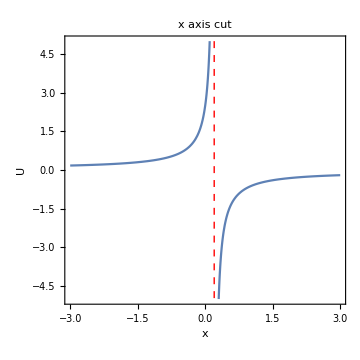

-Graphics3D-

```mathematica
c=0.1;q=-10;t=2;
Plot[{(c Coth[√(-c/q) (-c t+x)])/(2 √(-c/q) q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)]},{x,-3,3},PlotRange->{-5,5},PlotRange->All,Frame->True,

ExclusionsStyle->{{Dashed,Red},None},FrameLabel->{"x","U"},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},PlotLabel->"x axis cut",ImageSize->360]
setting1={ClippingStyle->None,ColorFunction->"Rainbow",Exclusions->"Singularities",PlotRange->Automatic,Boxed->False,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},AxesLabel->{"x","t","U"," "},PlotLabel->"3D Map",ViewPoint->{-1.71934700944275,2.426789012562308,1.613859024087029},ViewVertical->{0.2757186866254327,-0.38916581445508913,0.8789363883154763},ImageSize->360,AxesEdge->{{1,-1},{-1,-1},{1,1}},PlotStyle->Directive[Opacity[0.8],Thick,Red]};
Plot3D[
(c Coth[√(-c/q) (-c t+x)])/(2 √(-c/q) q)-1/2 √(-c/q) Tanh[√(-c/q) (-c t+x)]

,{x,-10,10},{t,0,1}
,Evaluate[setting1]
]
```

```mathematica
-Graphics3D-//AbsoluteOptions
```

{AlignmentPoint→Center,AspectRatio→0.724799,AutomaticImageSize→False,Axes→True,AxesEdge→{{1,-1},{-1,-1},{1,1}},AxesLabel→{FormBox["x",TraditionalForm],FormBox["t",TraditionalForm],FormBox["U",TraditionalForm]},AxesOrigin→{Automatic,Automatic,Automatic},AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→{1,1,0.4},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FaceGrids→None,FaceGridsStyle→Automatic,FormatType→TraditionalForm,ImageMargins→0.,ImagePadding→{{28.0157,12.2195},{16.4593,0.}},ImageSize→{347.278,249.615},ImageSizeRaw→Automatic,LabelStyle→{FontSize→13,FontFamily→Helvetica,GrayLevel[0]},Lighting→Neutral,Method→{DefaultBoundaryStyle→Directive[GrayLevel[0.3]],DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},RotationControl→Globe},PlotLabel→FormBox["3D Map",TraditionalForm],PlotRange→{{-10.,10.},{0.,1.},{-0.654663,0.651825}},PlotRangePadding→{{0.416667,0.416667},{0.0208333,0.0208333},{0.0272185,0.0272185}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→Automatic,Ticks→{{{-10.,-10,{0.00700665,0.}},{-9.,,{0.00420399,0.}},{-8.,,{0.00420399,0.}},{-7.,,{0.00420399,0.}},{-6.,,{0.00420399,0.}},{-5.,-5,{0.00700665,0.}},{-4.,,{0.00420399,0.}},{-3.,,{0.00420399,0.}},{-2.,,{0.00420399,0.}},{-1.,,{0.00420399,0.}},{0.,0,{0.00700665,0.}},{1.,,{0.00420399,0.}},{2.,,{0.00420399,0.}},{3.,,{0.00420399,0.}},{4.,,{0.00420399,0.}},{5.,5,{0.00700665,0.}},{6.,,{0.00420399,0.}},{7.,,{0.00420399,0.}},{8.,,{0.00420399,0.}},{9.,,{0.00420399,0.}},{10.,10,{0.00700665,0.}}},{{0.,0.0,{0.00966702,0.}},{0.05,,{0.00580021,0.}},{0.1,,{0.00580021,0.}},{0.15,,{0.00580021,0.}},{0.2,0.2,{0.00966702,0.}},{0.25,,{0.00580021,0.}},{0.3,,{0.00580021,0.}},{0.35,,{0.00580021,0.}},{0.4,0.4,{0.00966702,0.}},{0.45,,{0.00580021,0.}},{0.5,,{0.00580021,0.}},{0.55,,{0.00580021,0.}},{0.6,0.6,{0.00966702,0.}},{0.65,,{0.00580021,0.}},{0.7,,{0.00580021,0.}},{0.75,,{0.00580021,0.}},{0.8,0.8,{0.00966702,0.}},{0.85,,{0.00580021,0.}},{0.9,,{0.00580021,0.}},{0.95,,{0.00580021,0.}},{1.,1.0,{0.00966702,0.}}},{{-0.65,,{0.00580021,0.}},{-0.6,-0.6,{0.00966702,0.}},{-0.55,,{0.00580021,0.}},{-0.5,,{0.00580021,0.}},{-0.45,,{0.00580021,0.}},{-0.4,-0.4,{0.00966702,0.}},{-0.35,,{0.00580021,0.}},{-0.3,,{0.00580021,0.}},{-0.25,,{0.00580021,0.}},{-0.2,-0.2,{0.00966702,0.}},{-0.15,,{0.00580021,0.}},{-0.1,,{0.00580021,0.}},{-0.05,,{0.00580021,0.}},{0.,0.0,{0.00966702,0.}},{0.05,,{0.00580021,0.}},{0.1,,{0.00580021,0.}},{0.15,,{0.00580021,0.}},{0.2,0.2,{0.00966702,0.}},{0.25,,{0.00580021,0.}},{0.3,,{0.00580021,0.}},{0.35,,{0.00580021,0.}},{0.4,0.4,{0.00966702,0.}},{0.45,,{0.00580021,0.}},{0.5,,{0.00580021,0.}},{0.55,,{0.00580021,0.}},{0.6,0.6,{0.00966702,0.}},{0.65,,{0.00580021,0.}}}},TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{-1.71935,2.42679,1.61386},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0.275719,-0.389166,0.878936}}